```mathematica
<<"/Users/lucaarnaboldi/Desktop/staircase-ss/mathematica/Isserlis.m"
```

```mathematica
Omega
```

{{ω[1,1],ω[1,2],ω[1,3],ω[1,4],ω[1,5],ω[1,6],0},{ω[1,2],ω[2,2],ω[2,3],ω[2,4],ω[2,5],ω[2,6],0},{ω[1,3],ω[2,3],ω[3,3],ω[3,4],ω[3,5],ω[3,6],0},{ω[1,4],ω[2,4],ω[3,4],ω[4,4],ω[4,5],ω[4,6],0},{ω[1,5],ω[2,5],ω[3,5],ω[4,5],ω[5,5],ω[5,6],0},{ω[1,6],ω[2,6],ω[3,6],ω[4,6],ω[5,6],ω[6,6],0},{0,0,0,0,0,0,Δ}}

```mathematica
(*l = 1*)
(*I2noise = Expand[1]
I2 = Expand[(lf[1])*(lf[2])]
I3 = Expand[(1)*lf[2]*(lf[3])]
I4 = Expand[(1)*(1)*(lf[3])*(lf[4])]*)

(*l=2*)
I2noise = Expand[(2*lf[1])*(2*lf[2])]
I2 = Expand[(lf[1]^2-1)*(lf[2]^2-1)]
I3 = Expand[2*lf[1]*lf[2]*(lf[3]^2-1)]
I4 = Expand[(2*lf[1])*(2*lf[2])*(lf[3]^2-1)*(lf[4]^2-1)]

(*l=3*)
(*I2noise = Expand[(3*lf[1]^2-3)*(3*lf[2]^2-3)]
I2 = Expand[(lf[1]^3-3*lf[1])*(lf[2]^3-3*lf[2])]
I3 = Expand[(3*lf[1]^2-3)*lf[2]*(lf[3]^3-3*lf[3])]
I4 = Expand[(3*lf[1]^2-3)*(3*lf[2]^2-3)*(lf[3]^3-3*lf[3])*(lf[4]^3-3*lf[4])]*)

(*l=4*)
(*I2noise = Expand[(4*lf[1]^3-12*lf[1])*(4*lf[2]^3-12*lf[2])]
I2=Expand[(lf[1]^4-6*lf[1]^2+3)*(lf[2]^4-6*lf[2]^2+3)]
I3 = Expand[(4*lf[1]^3-12*lf[1])*lf[2]*(lf[3]^4-6*lf[3]^2+3)]
I4 = Expand[(4*lf[1]^3-12*lf[1])*(4*lf[2]^3-12*lf[2])*(lf[3]^4-6*lf[3]^2+3)*(lf[4]^4-6*lf[4]^2+3)]*)

(*l=5*)
(*I3 = Expand[(5*lf[1]^4-30*lf[1]^2+15)*lf[2]*(lf[3]^5-10*lf[3]^3+15*lf[3])]*)
(*I4 = Expand[(5*lf[1]^4-30*lf[1]^2+15)*(5*lf[2]^4-30*lf[2]^2+15)*(lf[3]^5-10*lf[3]^3+15*lf[3])*(lf[4]^5-10*lf[4]^3+15*lf[4])]*)

(*l=6*)
(*I3 = Expand[(6*lf[1]^5-60*lf[1]^3+90*lf[1])*lf[2]*(lf[3]^6-15*lf[3]^4+45*lf[3]^2-15)]*)
(*I4 = Expand[(6*lf[1]^5-60*lf[1]^3+90*lf[1])*(6*lf[2]^5-60*lf[2]^3+90*lf[2])*(lf[3]^6-15*lf[3]^4+45*lf[3]^2-15)*(lf[4]^6-15*lf[4]^4+45*lf[4]^2-15)]*)
```

4 λ[1] λ[2]

1-λ[1]^2-λ[2]^2+λ[1]^2 λ[2]^2

-2 λ[1] λ[2]+2 λ[1] λ[2] λ[3]^2

4 λ[1] λ[2]-4 λ[1] λ[2] λ[3]^2-4 λ[1] λ[2] λ[4]^2+4 λ[1] λ[2] λ[3]^2 λ[4]^2

```mathematica
Psit =IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->m, ω[1,3]->m,ω[2,2]->ρ,ω[2,3]->ρ,ω[3,3]->ρ} ;
Psis= IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->m, ω[1,3]->q,ω[2,2]->ρ,ω[2,3]->m,ω[3,3]->q} ;
(*Psis = 0;*)
PhiHDtt = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->m,ω[1,4]->m,ω[2,2]->q,ω[2,3]->m,ω[2,4]->m,ω[3,3]->ρ,ω[3,4]->ρ,ω[4,4]->ρ} ;
PhiHDss = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[1,4]->q,ω[2,2]->q,ω[2,3]->q,ω[2,4]->q,ω[3,3]->q,ω[3,4]->q,ω[4,4]->q} ;
(*PhiHDss = 0;*)
PhiHDts = IsserlisTheorem[I4] /. {ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[1,4]->m,ω[2,2]->q,ω[2,3]->q,ω[2,4]->m,ω[3,3]->q,ω[3,4]->m,ω[4,4]->ρ} ;
(*PhiHDts = 0;*)
PhiHDnoise = IsserlisTheorem[I2noise] /. {ω[1,1]->q,ω[1,2]->m,ω[2,2]->ρ};
PhiGFt =IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->q, ω[1,3]->m,ω[2,2]->q,ω[2,3]->m,ω[3,3]->ρ} ;
PhiGFs= IsserlisTheorem[I3] /.{ω[1,1]->q, ω[1,2]->q, ω[1,3]->q,ω[2,2]->q,ω[2,3]->q,ω[3,3]->q} ;
(*PhiGFs=0;*)
Riskss =IsserlisTheorem[I2] /.{ω[1,1]->q,ω[1,2]->q,ω[2,2]->q};
(*Riskss = 0;*)
Risktt = IsserlisTheorem[I2] /.{ω[1,1]->ρ,ω[1,2]->ρ,ω[2,2]->ρ};
Riskts = IsserlisTheorem[I2] /.{ω[1,1]->q,ω[1,2]->m,ω[2,2]->ρ};
(*Riskts = 0;*)
Pinv = 1/ρ;
Qorthinv = 1/(q-m^2/ρ);
GFM = FullSimplify[(Psit-Psis)];
GFQ = FullSimplify[(PhiGFt-PhiGFs)];
GFQorth = FullSimplify[GFQ - m*Pinv*GFM];
HDQ = (PhiHDtt+PhiHDss-2*PhiHDts+Δ*PhiHDnoise);
mUpdate =γ*GFM
qUpdate = FullSimplify[2*γ*GFQ+γ^2*1/α*HDQ+γ^2*ind*(GFM*Pinv*GFM)+γ^2*ind*(GFQorth*Qorthinv*GFQorth)]
PopRisk = 1/2*(Riskss +Risktt-2*Riskts)
```

6 m γ (-q+ρ)

1/α 4 γ (m γ Δ+2 m^2 (6 γ (-2 q+ρ)+α (1-6 ind q γ+4 ind γ ρ))+q (3 q^2 (5+3 ind α) γ-3 q (α+2 (1+ind α) γ ρ)+ρ (α+(3+ind α) γ ρ)))

1/2 (2-2 q+3 q^2-2 ρ+3 ρ^2-2 (1+2 m^2-q-ρ+q ρ))

```mathematica
mUpdateSpherical = Expand[FullSimplify[(mUpdate-m/2*qUpdate)/γ/.{ρ->1,q->1}]]
```

4 m-4 m^3-8 ind m γ+8 ind m^3 γ-(24 m γ)/α+(24 m^3 γ)/α-(2 m^2 γ Δ)/α

```mathematica
Psis
Psit
FullSimplify[GFM]
FullSimplify[HDQ/.{ρ->1,q->1}]
FullSimplify[(GFM*Pinv*GFM)/.{ρ->1,q->1}]
FullSimplify[GFQorth*Qorthinv*GFQorth/.{ρ->1,q->1}]
```

-2 m+6 m q

-2 m+6 m ρ

6 m (-q+ρ)

48+4 m (-12 m+Δ)

0

-16 (-1+m^2)

0.+4 x-0.4 ind x-4 x^3+0.4 ind x^3

1/2 (4-4 x^2)

0.-(4-0.4 ind) (-1/2+m^2/2)-(-4+0.4 ind) (-1/4+m^4/4)

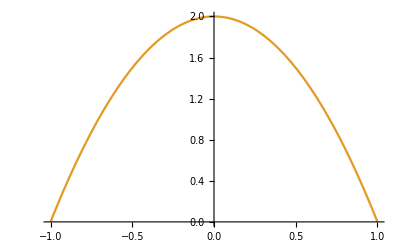

```mathematica
functionMUpdateSpherical[x_] = mUpdateSpherical /. {ρ->1,q->1,m->x, γ->.05,Δ->0, α->+Infinity}
functionPopRisk[x_] =PopRisk /.{ρ->1,q->1,m ->x,Δ->0}
EffectivePontentialSGD[m_]= -Integrate[functionMUpdateSpherical[x], {x,1,m}]
Plot[{EffectivePontentialSGD[m],functionPopRisk[m]},{m,-1,1}]
```

```mathematica
FortranForm[IsserlisTheorem[I3]/.{ω[1,1]->Caa,ω[1,2]->Cab, ω[1,3]->Cac,ω[1,4]->Cad,ω[2,2]->Cbb,ω[2,3]->Cbc, ω[2,4]->Cbd,ω[3,3]->Ccc,ω[3,4]->Ccd,ω[4,4]->Cdd}]
```

-2*Cab + 4*Cac*Cbc + 2*Cab*Ccc

```mathematica
FortranForm[mUpdateSpherical ]
```

4*m - 4*m**3 - 8*ind*m*γ + 8*ind*m**3*γ - (24*m*γ)/α + 
     -  (24*m**3*γ)/α - (2*m**2*γ*Δ)/α